```mathematica
replace[str_String,s_STring:"±"]:=ToExpression@Partition[StringReplace[StringSplit[str],s->""]/.""->Nothing,2]
```

```mathematica
data1=replace["4.07 ± 1.61 3.20 ± 1.17 2.94 ± 1.12 3.78 ± 0.87 2.35 ± 1.28 2.03 ± 1.07 2.29 ± 0.51 2.18 ± 0.47 1.72 ± 0.83 3.56 ± 0.75 2.83 ± 0.59 10.41 ± 1.81 4.29 ± 1.01 5.64 ± 1.49 2.67 ± 1.02 2.29 ± 0.19 3.47 ± 0.99 2.16 ± 1.01 22.78 ± 2.58 13.52 ± 1.51 11.18 ± 2.91 6.40 ± 1.17 5.15 ± 2.24 2.30 ± 0.27 2.61 ± 0.58 3.68 ± 0.49 2.22 ± 0.90 11.88 ± 2.99 5.97 ± 2.14 4.44 ± 0.59 3.92 ± 1.24 2.55 ± 1.11 5.35 ± 1.46 2.17 ± 1.61"];
```

```mathematica
data2=replace["10.21 ± 2.76 1.89 ± 1.26 6.09 ± 3.16 7.23 ± 3.51 5.90 ± 4.90 0.11 ± 0.16 1.92 ± 2.20 0.34 ± 0.40 6.76 ± 1.47 0.14 ± 0.22 3.67 ± 1.37 21.26 ± 11.9 13.38 ± 5.67 6.28 ± 0.85 5.63 ± 0.61 20.28 ± 9.79 9.30 ± 2.28 5.67 ± 1.35 32.27 ± 9.91 15.95 ± 1.79 18.52 ± 14.63 8.89 ± 1.82 19.47 ± 7.45 12.86 ± 4.80 2.43 ± 0.55 4.52 ± 0.96 6.12 ± 1.99 24.59 ± 8.28 21.10 ± 1.89 18.30 ± 9.26 2.02 ± 2.07 3.32 ± 1.19 16.74 ± 3.65 7.45 ± 4.17"];
```

```mathematica
data3=replace["17.12 ± 1.87 15.42 ± 5.10 11.00 ± 1.36 12.30 ± 2.72 9.20 ± 3.53 39.51 ± 17.94 9.26 ± 2.08 10.78 ± 2.99 8.28 ± 1.12 13.28 ± 7.89 12.75 ± 2.78 47.24 ± 28.68 13.62 ± 5.92 12.45 ± 3.01 18.82 ± 9.96 7.60 ± 7.49 16.01 ± 7.58 7.96 ± 1.21 53.5 ± 4.78 43.91 ± 11.72 27.94 ± 9.43 25.93 ± 17.2 42.09 ± 18.84 17.39 ± 12.86 4.36 ± 0.51 8.28 ± 4.79 26.29 ± 2.09 16.18 ± 8.47 73.39 ± 10.22 37.43 ± 13.34 12.69 ± 3.52 6.87 ± 0.61 29.06 ± 9.35 8.55 ± 6.37"];
```

```mathematica
data4=replace["0.30 ± 0.05 0.18 ± 0.06 0.26 ± 0.05 0.16 ± 0.05 0.20 ± 0.05 0.14 ± 0.06 0.20 ± 0.06 0.06 ± 0.06 0.33 ± 0.04 0.35 ± 0.03 0.32 ± 0.03 0.36 ± 0.08 1.20 ± 0.03 1.39 ± 0.06 0.44 ± 0.03 1.08 ± 0.78 1.64 ± 0.00 0.36 ± 0.01 3.30 ± 0.10 3.40 ± 0.00 2.28 ± 0.08 3.04 ± 0.05 1.40 ± 0.05 0.49 ± 0.12 0.95 ± 0.25 0.40 ± 0.02 0.39 ± 0.02 3.70 ± 0.00 3.70 ± 0.00 0.81 ± 0.03 1.88 ± 0.25 1.06 ± 0.04 1.92 ± 0.13 0.74 ± 0.10"];
```

```mathematica
data5=replace["0.36 ± 0.05
0.26 ± 0.05
0.24 ± 0.05 0.30 ± 0.05 0.24 ± 0.05 0.32 ± 0.05 0.26 ± 0.05 0.18 ± 0.05 0.60 ± 0.05 0.60 ± 0.04 0.68 ± 0.13 1.28 ± 0.22 0.99 ± 0.07 3.70 ± 0.†0 1.90 ± 0.06 3.31 ± 0.13 3.06 ± 0.09 1.10 ± 0.01 5.85 ± 2.31 6.50 ± 2.24 5.70 ± 0.20 7.40 ± 0.00 1.53 ± 0.18 1.26 ± 0.07 1.25 ± 0.20 1.52 ± 0.03 1.24 ± 0.01 7.40 ± 0.00 7.40 ± 0.00 3.21 ± 0.07 3.32 ± 0.08 1.64 ± 0.00 3.37 ± 0.10 1.00 ± 0.09"];
```

```mathematica
data6=replace["0.34 ± 0.06 0.38 ± 0.15 0.32 ± 0.06 0.24 ± 0.06 0.40 ± 0.06 0.48 ± 0.15 0.36 ± 0.15 0.66 ± 0.15 0.84 ± 0.07 0.93 ± 0.16 1.56 ± 0.06 4.62 ± 0.24 1.77 ± 0.20 6.46 ± 0.17 4.68 ± 0.22 6.00 ± 0.30 6.17 ± 0.12 1.60 ± 0.00 8.67 ± 0.56 8.33 ± 0.39 8.41 ± 0.74 10.57 ± 0.15 3.70 ± 0.00 0.94 ± 0.10 2.90 ± 0.74 3.32 ± 0.11 2.84 ± 0.07 8.27 ± 0.09 8.23 ± 0.30 7.26 ± 0.17 7.40 ± 0.00 4.60 ± 0.41 5.67 ± 0.12 1.04 ± 0.09"];
```

```mathematica
data={data1,data2,data3,data4,data5,data6};
```

```mathematica
IPFP[{{a_,b_},{c_,d_},{e_,f_}}]:=b+(-a+#) ((-b+d)/(-a+c)+((-(-b+d)/(-a+c)+(-d+f)/(-c+e)) (-c+#))/(-a+e))&
```

```mathematica
data7=Transpose[{data4[[All,1]],data5[[All,1]],data6[[All,1]]}];
```

```mathematica
data8=Transpose[{data1[[All,1]],data2[[All,1]],data3[[All,1]]}];
```

```mathematica
temperaturedata=ToExpression@Import["./Desktop/temperaturedata.txt"];
```

```mathematica
ipflist=IPFP/@#&/@MapThread[{#1,#2}&,({{10,#1},{16,#2},{22,#3}}&@@@#&/@({#,MapThread[#3*#2/(122*#1)&,{data7,data8,#}]}&@(Log[122*#+1]/122&/@data7)))];
```

### 一年天气变化范围图

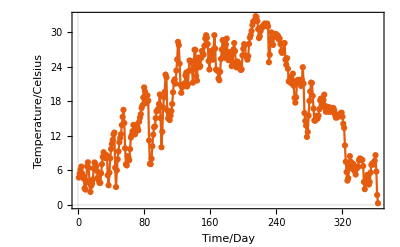

```mathematica
ListLinePlot[temperaturedata,Mesh->All,PlotTheme->"Scientific",FrameLabel->{"Time/Day","Temperature/Celsius"}]
```

### 120天天气变化范围

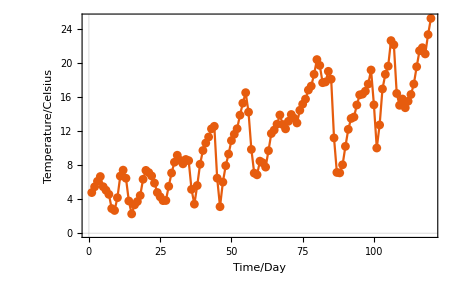

```mathematica
ListLinePlot[temperaturedata[[;;120]],Mesh->All,PlotTheme->"Scientific",FrameLabel->{"Time/Day","Temperature/Celsius"}]
```

```mathematica
ip=Interpolation[temperaturedata];
```

### 对应气候条件下无竞争模型真菌群有机物分解率

```mathematica
decompositionrate1=FoldList[Plus,0,MapThread[#1.#2&,{Table[Through[ipflist[[All,2]][ip[x+1]]],{x,0,120}],FoldList[Plus,ConstantArray[1,34],Table[(Through[ipflist[[All,1]][ip[x]]]*E^(Through[ipflist[[All,1]][ip[x]]]*x)),{x,120}]]}]];
```

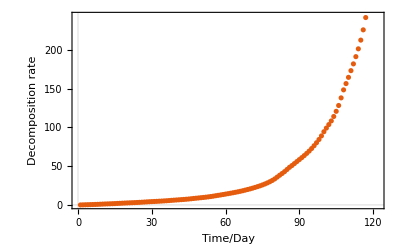

```mathematica
ListPlot[decompositionrate1,PlotTheme->"Scientific",FrameLabel->{"Time/Day","Decomposition rate"}]
```

我们可以假设前80天可以表现真实情况，用逻辑回归模型拟合

```mathematica
logit=Normal@LogitModelFit[decompositionrate1[[;;80]]/100,x,x];
```

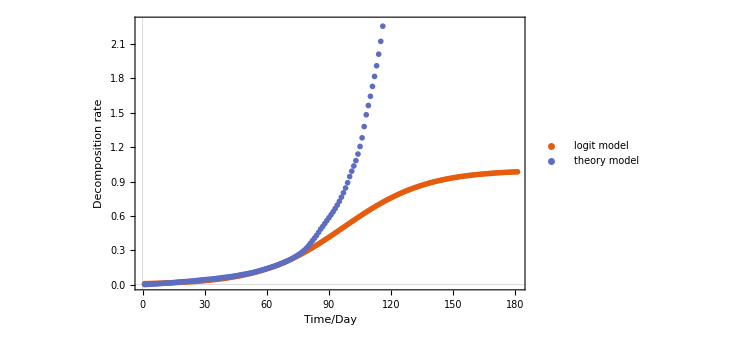

```mathematica
ListPlot[{Table[logit,{x,0,180}],decompositionrate1/100},PlotTheme->"Scientific",PlotLegends->Placed[PointLegend[{"logit model","theory model"},LegendFunction->"Frame",LegendLayout->"Column",LegendMarkerSize->25],{{0.3,0.8},{0.4,1}}],FrameLabel->{"Time/Day","Decomposition rate"}]
```

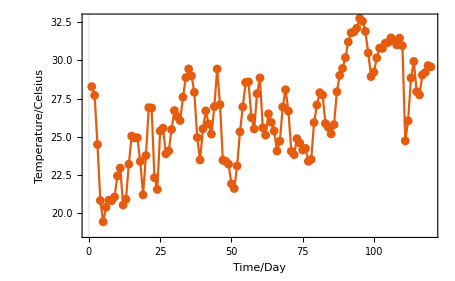

```mathematica
ListLinePlot[temperaturedata[[121;;240]],Mesh->All,PlotTheme->"Scientific",FrameLabel->{"Time/Day","Temperature/Celsius"}]
```

### 对应气候条件下无竞争模型真菌群有机物分解率

```mathematica
decompositionrate2=FoldList[Plus,0,MapThread[#1.#2&,{Table[Through[ipflist[[All,2]][ip[x+120]]],{x,0,120}],FoldList[Plus,ConstantArray[1,34],Table[(Through[ipflist[[All,1]][ip[x+120]]]*E^(Through[ipflist[[All,1]][ip[x+120]]]*x)),{x,120}]]}]];
```

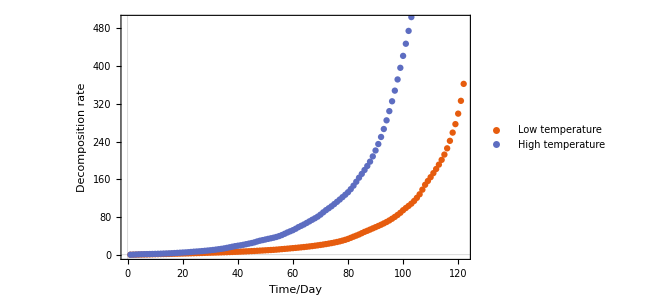

```mathematica
ListPlot[{decompositionrate1,decompositionrate2},PlotTheme->"Scientific",FrameLabel->{"Time/Day","Decomposition rate"},PlotLegends->Placed[PointLegend[{"Low temperature","High temperature"},LegendFunction->"Frame",LegendLayout->"Column",LegendMarkerSize->20],{{0.3,0.8},{0.4,1}}]]
```

我们可以假设前80天可以表现真实情况，用逻辑回归模型拟合

```mathematica
logit1=Normal@LogitModelFit[decompositionrate2[[;;60]]/100,x,x];
```

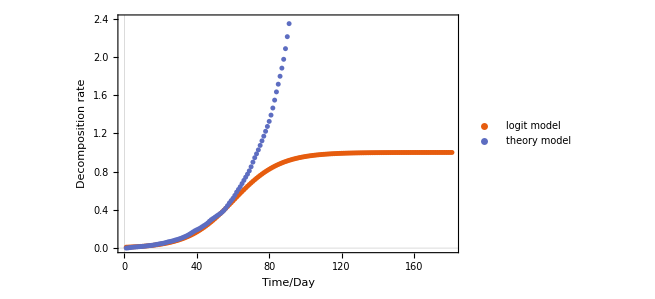

```mathematica
ListPlot[{Table[logit1,{x,0,180}],decompositionrate2/100},PlotTheme->"Scientific",PlotLegends->Placed[PointLegend[{"logit model","theory model"},LegendFunction->"Frame",LegendLayout->"Column",LegendMarkerSize->20],{{0.7,0.8},{0.4,1}}],FrameLabel->{"Time/Day","Decomposition rate"}]
```

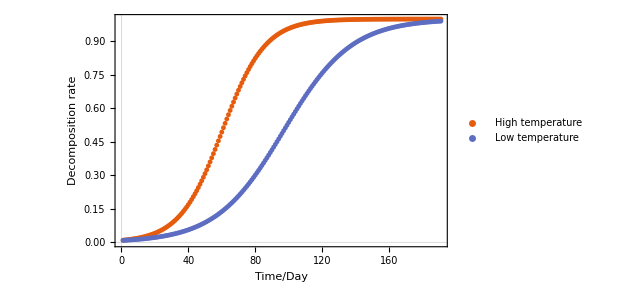

```mathematica
ListPlot[{Table[logit1,{x,0,190}],Table[logit,{x,0,190}]},PlotTheme->"Scientific",PlotLegends->Placed[PointLegend[{"High temperature ","Low temperature"},LegendFunction->"Frame",LegendLayout->"Column",LegendMarkerSize->20],{{0.7,0.8},{0.2,2.2}}],FrameLabel->{"Time/Day","Decomposition rate"}]
```

```mathematica
result[n_]:=Table[x[k],{k,34}]/.NDSolve[Join[Table[D[x[k][t],t]==ipflist[[k,1]][ip[t+1]]*x[k][t]*(1-(Table[x[k][t]/n,{k,34}].(Through[ipflist[[All,2]][ip[t+1]]]/ipflist[[1,2]][ip[t+1]]))),{k,1,34}],Table[x[k][0]==1,{k,34}]],Table[x[k],{k,1,34}],{t,0,360}][[1]]
```

```mathematica
decompositionratefunc[n_,m_]:=With[{mid=result[n]},FoldList[Plus,MapThread[#1.#2&,{Table[Through[ipflist[[All,2]][ip[x+1]]],{x,0,m}],Transpose@Through[mid[Range[0,m]]]}]]]
```

```mathematica
decompositionratedata=decompositionratefunc[#,360]&/@{500,1000,1500,2000};
```

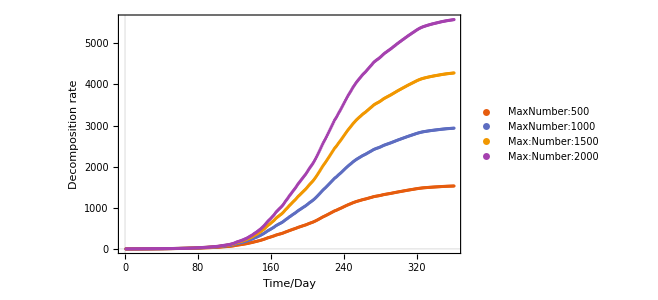

```mathematica
ListPlot[decompositionratedata,PlotTheme->"Scientific",PlotLegends->Placed[PointLegend[{"MaxNumber:500","MaxNumber:1000","Max:Number:1500","Max:Number:2000"},LegendFunction->"Frame",LegendLayout->"Column",LegendMarkerSize->15],{{0.2,0.8},{0.4,1}}],FrameLabel->{"Time/Day","Decomposition rate"}]
```

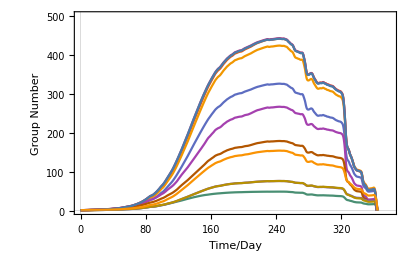

```mathematica
Plot[Evaluate[Through[result[1000][[20;;30]][x]]],{x,0,380},PlotRange->{{0,380},{0,500}},PlotTheme->"Scientific",FrameLabel->{"Time/Day","Group Number"}]
```

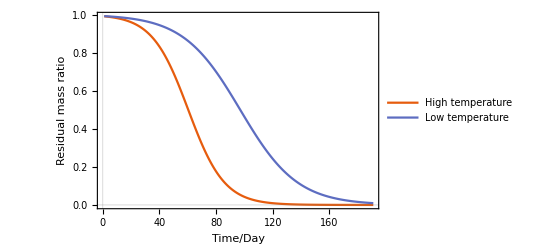

```mathematica
ListLinePlot[{Table[1-logit1,{x,0,190}],Table[1-logit,{x,0,190}]},PlotTheme->"Scientific",PlotLegends->Placed[PointLegend[{"High temperature ","Low temperature"},LegendFunction->"Frame",LegendLayout->"Column",LegendMarkerSize->15],{{0.6,0.8},{0.2,0.9}}],FrameLabel->{"Time/Day","Residual mass ratio "}]
```

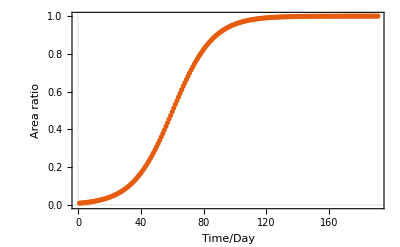

```mathematica
ListPlot[{Table[logit1,{x,0,190}]},PlotTheme->"Scientific",FrameLabel->{"Time/Day","Area ratio"}]
```